M（蛋氨酸铜) = 359.95 g / mol;
M（蛋氨酸）= 149.21 g / mol;
M（碘酸钾）= 214.00 g / mol;

```mathematica
(2.54/359.95)/(1.92/250)
```

0.91882

```mathematica
list1={17.52,17.56,17.54};
list2={{0.1037,15.05},{0.1029,15.02},{0.1044,14.94}};
list3={{0.1159,16.00},{0.1035,14.35},{0.1191,16.40}};
list4=Transpose[{First/@#,Last/@#-0.04}]&@list3;
```

```mathematica
list4
```

{{0.1159,15.96},{0.1035,14.31},{0.1191,16.36}}

```mathematica
TableForm[{{"",0.3341,""},#,0.3341/5*3/214.00/(#/1000)&/@#,{"",Mean[0.3341/5*3/214.00/(#/1000)&/@#],""},
{"",MeanDeviation[0.3341/5*3/214.00/(#/1000)&/@#],""},{"",MeanDeviation[#]/Mean[#]&[0.3341/5*3/214.00/(#/1000)&/@#]}}&[list1],TableHeadings->{{"m(KIO_3)/g","V(Na_2S_2O_3)/mL","1/2c(Na_2S_2O_3)/(mol/L)","1/2c̄(Na_2S_2O_3)/(mol/L)","相对偏差","相对平均偏差"},Range[3]}]
TableForm[Join[Transpose[list2],{0.025*0.09669/2-0.05341/1000*Last/@list2,Divide@@@Transpose[{149.21*(0.025*0.09669/2-0.05341/1000*Last/@list2),First/@list2}],{"",Mean[Divide@@@Transpose[{149.21*(0.025*0.09669/2-0.05341/1000*Last/@list2),First/@list2}]],""},{"",MeanDeviation[Divide@@@Transpose[{149.21*(0.025*0.09669/2-0.05341/1000*Last/@list2),First/@list2}]],""},
{"",MeanDeviation[#]/Mean[#]&[Divide@@@Transpose[{149.21*(0.025*0.09669/2-0.05341/1000*Last/@list2),First/@list2}]],""}}],TableHeadings->{{"m(产品)/g","V(Na_2S_2O_3)/mL","n(蛋氨酸)/mol","蛋氨酸相对含量","蛋氨酸平均相对含量","相对偏差","相对平均偏差"},Range[3]}]
TableForm[Join[Transpose[list3],{(Last/@list3)*0.05125/2.5/1000,Divide@@@Transpose[{63.546*(Last/@list3)*0.05125/2.5/1000,First/@list3}],{"",Mean[Divide@@@Transpose[{63.546*(Last/@list3)*0.05125/2.5/1000,First/@list3}]],""},{"",MeanDeviation[Divide@@@Transpose[{63.546*(Last/@list3)*0.05125/2.5/1000,First/@list3}]],""},{"",MeanDeviation[#]/Mean[#]&[Divide@@@Transpose[{63.546*(Last/@list3)*0.05125/2.5/1000,First/@list3}]],""}}],TableHeadings->{{"m(产品)/g","V(EDTA)/mL","n(Cu)/mol","Cu相对含量","Cu平均相对含量","相对偏差","相对平均偏差"},Range[3]}]
TableForm[Join[Transpose[list4],{(Last/@list4)*0.05125/2.5/1000,Divide@@@Transpose[{63.546*(Last/@list4)*0.05125/2.5/1000,First/@list4}],{"",Mean[Divide@@@Transpose[{63.546*(Last/@list4)*0.05125/2.5/1000,First/@list4}]],""},{"",MeanDeviation[Divide@@@Transpose[{63.546*(Last/@list4)*0.05125/2.5/1000,First/@list4}]],""},{"",MeanDeviation[#]/Mean[#]&[Divide@@@Transpose[{63.546*(Last/@list4)*0.05125/2.5/1000,First/@list4}]],""}}],TableHeadings->{{"m(产品)/g","V(EDTA)/mL","n(Cu)/mol","Cu相对含量","Cu平均相对含量","相对偏差","相对平均偏差"},Range[3]}]
```

| 1 | 2 | 3
m(KIO_3)/g |  | 0.3341 | 
V(Na_2S_2O_3)/mL | 17.52 | 17.56 | 17.54
1/2c(Na_2S_2O_3)/(mol/L) | 0.0534663 | 0.0533445 | 0.0534053
1/2c̄(Na_2S_2O_3)/(mol/L) |  | 0.0534053 | 
相对偏差 |  | 0.0000406124 | 
相对平均偏差 |  | 0.000760456 |

| 1 | 2 | 3
m(产品)/g | 0.1037 | 0.1029 | 0.1044
V(Na_2S_2O_3)/mL | 15.05 | 15.02 | 14.94
n(蛋氨酸)/mol | 0.00016308 | 0.000164682 | 0.000168955
蛋氨酸相对含量 | 0.234649 | 0.238797 | 0.241472
蛋氨酸平均相对含量 |  | 0.586239 | 
相对偏差 |  | 0.0025207 | 
相对平均偏差 |  | 0.00429979 |

| 1 | 2 | 3
m(产品)/g | 0.1159 | 0.1035 | 0.1191
V(EDTA)/mL | 16. | 14.35 | 16.4
n(Cu)/mol | 0.000328 | 0.000294175 | 0.0003362
Cu相对含量 | 0.179837 | 0.180615 | 0.17938
Cu平均相对含量 |  | 0.179944 | 
相对偏差 |  | 0.000447325 | 
相对平均偏差 |  | 0.00248591 |

| 1 | 2 | 3
m(产品)/g | 0.1159 | 0.1035 | 0.1191
V(EDTA)/mL | 15.76 | 14.11 | 16.16
n(Cu)/mol | 0.00032308 | 0.000289255 | 0.00033128
Cu相对含量 | 0.177139 | 0.177594 | 0.176755
Cu平均相对含量 |  | 0.177163 | 
相对偏差 |  | 0.000287581 | 
相对平均偏差 |  | 0.00162326 |

```mathematica
0.1795/63.55/(0.5862/149.21)
```

0.718954

```mathematica
0.177/63.55*359.95
```

1.00254

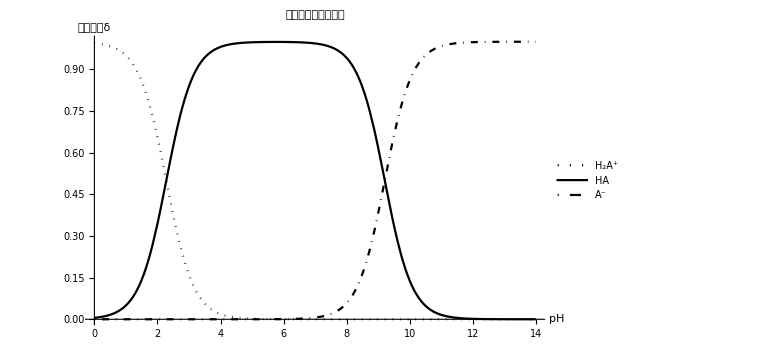

```mathematica
Plot[Evaluate[IonDistribution[10^-x,{10^-2.28,10^-9.21}]],{x,0,14},PlotLegends->{"H_2A^+","HA","A^-"},PlotLabel->Style["甲硫氨酸分布系数图",Black,16],PlotStyle->{{Black,Dotted},{Black},{Black,DotDashed}},AxesLabel->{"pH","分布系数δ"},LabelStyle->Black,ImageSize->Large]
```